## Base model - analytic

```mathematica
Lambda[rh_,mh_,re_,me_]:=1/2 (re+rh-me-mh+√((-re-rh+me+mh)^2-4 (re rh-re me-rh mh)))
```

```mathematica
DLDre[rh_,mh_,re_,me_]:=1/4 (2+(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDrh[rh_,mh_,re_,me_]:=1/4 (2-(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDmh[rh_,mh_,re_,me_]:=1/4 (-2+(2 (me+mh-re+rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDme[rh_,mh_,re_,me_]:=1/4 (-2+(2 (me+mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
Solve[-DLDmh[rho,m,1,m]==DLDrh[rho,m,1,m],m]
```

{{m→1-rho}}

## Base model + competition in the environment

```mathematica
eq1={D[nH[t],t]==rh*nH[t]-me*nH[t]+mh*nE[t],nH[0]==nH0}
```

{nH'[t]==mh nE[t]-me nH[t]+rh nH[t],nH[0]==nH0}

```mathematica
eq2={D[nE[t],t]==me*nH[t]+(re-mh)nE[t]-k*(nE[t])^2,nE[0]==nE0}
```

{nE'[t]==(-mh+re) nE[t]-k nE[t]^2+me nH[t],nE[0]==nE0}

```mathematica
sys={eq1,eq2}
```

{{nH'[t]==mh nE[t]-me nH[t]+rh nH[t],nH[0]==nH0},{nE'[t]==(-mh+re) nE[t]-k nE[t]^2+me nH[t],nE[0]==nE0}}

```mathematica
Biglambda[tmax_,nh0_,ne0_,nhf_,nef_]:=(1/tmax)*Log[(nhf+nef)/(nh0+ne0)];
```

## Functions definition

```mathematica
(*Function that takes all the Rempl parameters as arguments and returns a table of same format containing the final values of the numerical solution of the system of equations:*)
```

```mathematica
SolutionCalc[Rempl_,nE0t_,nH0t_]:=(Module[{tabT,TabRHO,TabM,TabK},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;Table[{nE[tabT[[itmax]]],nH[tabT[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->nE0t/.nH0->nH0t,{nE,nH},{t,0,tabT[[itmax]]}],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}]])
```

```mathematica
(*Function that takes all the Rempl parameters AND the solution as arguments and returns the lambda values in a table of same format as Rempl*)
```

```mathematica
LambdaCalc[Rempl_,Solu_,nE0t_,nH0t_]:=(Module[{tabT,TabRHO,TabM,TabK},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
Table[Biglambda[tabT[[itmax]], nH0t,nE0t,Solu⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,Solu⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}]])
```

```mathematica
(*Function that takes as argument the parameters Rempl and returns a list of {the solution, the corresponding lambda, sensi1,sensi2,sensi3,...}*)
```

```mathematica
SensitivityCalc[Rempl_,nE0t_,nH0t_,α_]:=(Module[{tabT,RE,TabRHO,TabM,TabK,Solu,DTabRHO,DTabM,DRHRempl,DMERempl,DMHRempl,DRHSol,DMESol,DMHSol,Lambda,DRHLambda,DMELambda,DMHLambda,SensiRH,SensiRE,SensiMH,SensiME,SensiK,TabRHdim,TabMdim},

tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
RE = Rempl⟦1,;;,1,1,2⟧[[1,2]];

TabRHdim=Table[TabRHO[[irho]],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
TabMdim=Table[TabM[[im]],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

Solu = SolutionCalc[Rempl,nE0t,nH0t];

DTabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧+α;
DTabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧+α;

DRHRempl =Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> DTabRHO⟦irho⟧,me->TabM⟦im⟧,mh->TabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
DMERempl = Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> TabRHO⟦irho⟧,me->DTabM⟦im⟧,mh->TabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
DMHRempl = Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> TabRHO⟦irho⟧,me->TabM⟦im⟧,mh->DTabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

DRHSol = SolutionCalc[DRHRempl,nE0t,nH0t];
DMESol = SolutionCalc[DMERempl,nE0t,nH0t];
DMHSol = SolutionCalc[DMHRempl,nE0t,nH0t];

Lambda = LambdaCalc[Rempl,Solu,nE0t,nH0t];
DRHLambda = LambdaCalc[DRHRempl,DRHSol,nE0t,nH0t];
DMELambda = LambdaCalc[DMERempl,DMESol,nE0t,nH0t];
DMHLambda = LambdaCalc[DMHRempl,DMHSol,nE0t,nH0t];

SensiRH =(1/α)*(DRHLambda-Lambda);
SensiME =(1/α)*(DMELambda-Lambda);
SensiMH =(1/α)*(DMHLambda-Lambda);

{Solu,Lambda,SensiRH,SensiME,SensiMH}]

)
```

```mathematica
(*Function that takes Rempl as an argument and returns {Sensitivities (format of the previous function),Optimal strategies (of same format as Rempl)}.*)
```

```mathematica
OptimalStrategy[Rempl_,nE0t_,nH0t_,α_]:=(Module[{tabT,TabRHO,TabM,TabK,RE,Sensitivities,SensiRH,SensiME,SensiMH,Opt},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
RE = Rempl⟦1,;;,1,1,2⟧[[1,2]];

Sensitivities = SensitivityCalc[Rempl,nE0t,nH0t,α];
SensiRH = Sensitivities[[3]];
SensiME = Sensitivities[[4]];
SensiMH = Sensitivities[[5]];

Opt=Table[Sign[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}⟦Position[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}],Max[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}]]]⟦1,1⟧⟧]*Position[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}],Max[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}]]]⟦1,1⟧,{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

{Sensitivities,Opt}])
```

### Equilibrium

```mathematica
eq1W=0==rE*nE-mH*nE+mE*nH-k*nE*nE
```

0==-mH nE-k nE^2+mE nH+nE rE

```mathematica
eq2W=0==rH*nH-mE*nH+mH*nE
```

0==mH nE-mE nH+nH rH

```mathematica
sysW={eq1W,eq2W}
```

{0==-mH nE-k nE^2+mE nH+nE rE,0==mH nE-mE nH+nH rH}

```mathematica
SolW=FullSimplify[Solve[sysW,{nE,nH}]]
```

{{nE→0,nH→0},{nE→(mE rE+mH rH-rE rH)/(k mE-k rH),nH→(mH (mE rE+(mH-rE) rH))/(k (mE-rH)^2)}}

```mathematica
(*There is the null solution, and then the only potentially positive solution*)
```

```mathematica
nEW[rE_,rH_,mE_,mH_]:=(mE rE+mH rH-rE rH)/(k mE-k rH)
```

```mathematica
nHW[rE_,rH_,mE_,mH_]:=(mH (mE rE+(mH-rE) rH))/(k (mE-rH)^2)
```

```mathematica
(*It is actually easy to look at the sign of those equilibria analytically (and also to calculate them). First of all, we have nHW=(mh/(me-rh))nEW. Which means, since we only consider positive m, that if we want both of them to be positive at the same time then we need rh<me. Then we can look at the positivity of just nEW. On our parameter space of interest (equal mh=me, re=1), since k is positive we find that nEW is positive if m+rho(m-1)>0 ie m>rho/(1+rho). Let us look at  *)
```

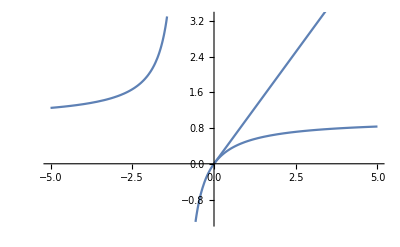

```mathematica
Show[Plot[rho/(1+rho),{rho,-5,5}],Plot[rho,{rho,0,10}]]
```

```mathematica
(*For the region of the parameter space we are interested in (rho>-1) the condition m>rho is thus sufficient for the existence of a positive equilibrium. Intuitively it makes sense: if migration is so important that microbes migrate out of the host faster than they replicate in it (m>rH) then the exponential growth never truly has the time to kick in and competition is efficient everywhere despite formally existing only in the host. If migration is smaller than replication though, we DO have dnH/dt always positive, and a population that explodes in the environment. Let us check with some dynamics below*)
```

### Sensitivity of the final pop size

```mathematica
popFinal[rE_,rH_,mE_,mH_]:=nEW[rE,rH,mE,mH]+nHW[rE,rH,mE,mH]
```

```mathematica
Simplify[D[popFinal[rE,rH,mE,mH],rH]]/.rE->1/.mE->m/.mH->m
```

(m (m^2+m (1+m-rH)+(-1+m) rH))/(k (m-rH)^3)

```mathematica
Simplify[D[popFinal[rE,rH,mE,mH],mH]]/.rE->1/.mE->m/.mH->m
```

((-1+2 m-rH) rH+m (1+rH))/(k (m-rH)^2)

```mathematica
DLDRHO[rH_,m_]:=(m (m^2+m (1+m-rH)+(-1+m) rH))/(k (m-rH)^3)
```

```mathematica
DLDM[rH_,m_]:=((-1+2 m-rH) rH+m (1+rH))/(k (m-rH)^2)
```

```mathematica
Sol=Refine[Solve[-DLDM[rho,m]==DLDRHO[rho,m],m],m>0&&rho>-1&&rho<1]
```

{{m→rho/2},{m→1/2 (-1-2 rho-√(1+8 rho+8 rho^2))},{m→1/2 (-1-2 rho+√(1+8 rho+8 rho^2))}}

```mathematica
(*Does not depend on k!*)
```

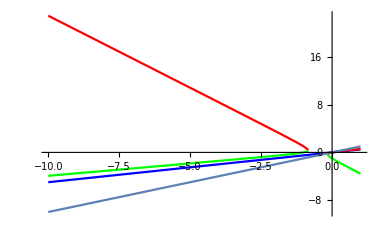

```mathematica
Show[Plot[{m/.Sol[[1]],m/.Sol[[2]],m/.Sol[[3]]},{rho,-10,1},PlotRange->All,PlotStyle->{Blue,Green,Red}],Plot[rho,{rho,-10,1}]]
```

```mathematica
(*We only keep what is above the m>rho line*)
```

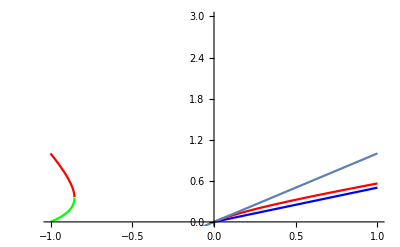

```mathematica
Show[Plot[{m/.Sol[[1]],m/.Sol[[2]],m/.Sol[[3]]},{rho,-1,1},PlotRange->{{-1,1},{0,3}},PlotStyle->{Blue,Green,Red}],Plot[rho,{rho,-10,1}]]
```

```mathematica
(*we only keep the left branch becaue the rest is below m=rho, thus where there is no positive equilibrium*)
```

```mathematica
(*Now what about the other contour, -1?*)
```

```mathematica
Sol2=Refine[Solve[-DLDM[rho,m]==-DLDRHO[rho,m],m],m>0&&rho>-1&&rho<1]
```

{{m→rho/2-(6 rho+15 rho^2)/(6 3^(1/3) (9 rho^2-9 rho^3+√3 √(8 rho^3+87 rho^4+96 rho^5+152 rho^6))^(1/3))+((9 rho^2-9 rho^3+√3 √(8 rho^3+87 rho^4+96 rho^5+152 rho^6))^(1/3))/(2 3^(2/3))},{m→rho/2+((1+ⅈ √3) (6 rho+15 rho^2))/(12 3^(1/3) (9 rho^2-9 rho^3+√3 √(8 rho^3+87 rho^4+96 rho^5+152 rho^6))^(1/3))-((1-ⅈ √3) (9 rho^2-9 rho^3+√3 √(8 rho^3+87 rho^4+96 rho^5+152 rho^6))^(1/3))/(4 3^(2/3))},{m→rho/2+((1-ⅈ √3) (6 rho+15 rho^2))/(12 3^(1/3) (9 rho^2-9 rho^3+√3 √(8 rho^3+87 rho^4+96 rho^5+152 rho^6))^(1/3))-((1+ⅈ √3) (9 rho^2-9 rho^3+√3 √(8 rho^3+87 rho^4+96 rho^5+152 rho^6))^(1/3))/(4 3^(2/3))}}

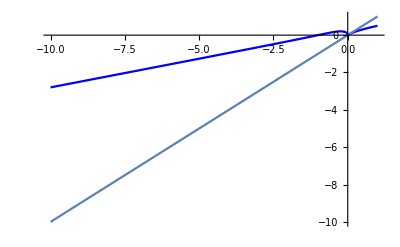

```mathematica
Show[Plot[{m/.Sol2[[1]],m/.Sol2[[2]],m/.Sol2[[3]]},{rho,-10,1},PlotRange->All,PlotStyle->{Blue,Green,Red}],Plot[rho,{rho,-10,1}]]
```

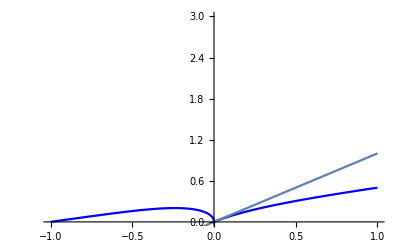

```mathematica
Show[Plot[{m/.Sol2[[1]],m/.Sol2[[2]],m/.Sol2[[3]]},{rho,-1,1},PlotRange->{{-1,1},{0,3}},PlotStyle->{Blue,Green,Red}],Plot[rho,{rho,-10,1}]]
```

```mathematica
(*We keep the left branch there too!*)
```

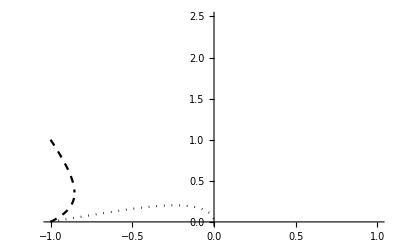

```mathematica
Limits=Show[Plot[m/.Sol2[[1]],{rho,-1,0},PlotRange->{{-1,1},{0,2.5}},PlotStyle->Directive[Black,Dotted,Thickness[0.004]]],Plot[{m/.Sol[[1]],m/.Sol[[2]],m/.Sol[[3]]},{rho,-1,0},PlotRange->{{-1,1},{0,2.5}},PlotStyle->Directive[Black,Dashed,Thickness[0.004]]]]
```

## Supplementary figure 4 - panel C

```mathematica
tmaxB = {30};
NE0 =1;
NH0 = 0;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.15,2.5,0.05}]}];
TabKH =10^-{11,9,7,5,3,1};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatA=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatA[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{1}
 |  |  |  |

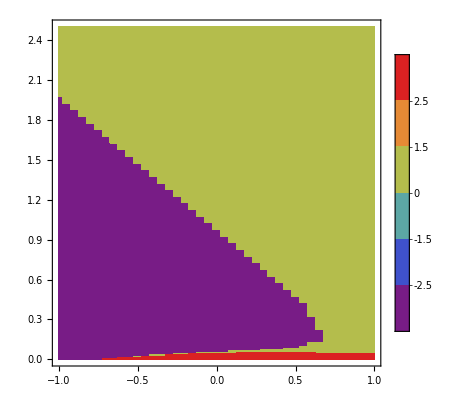
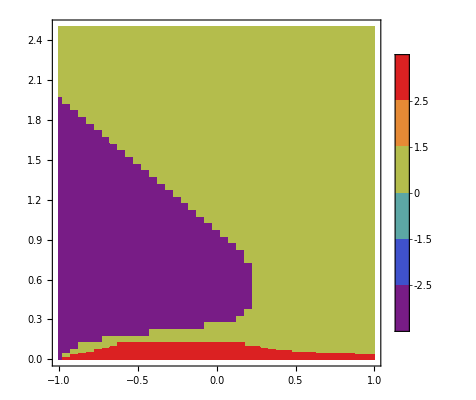
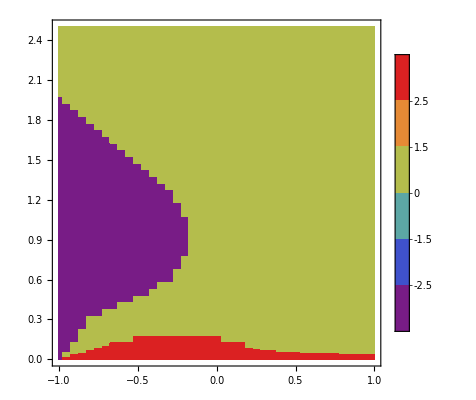
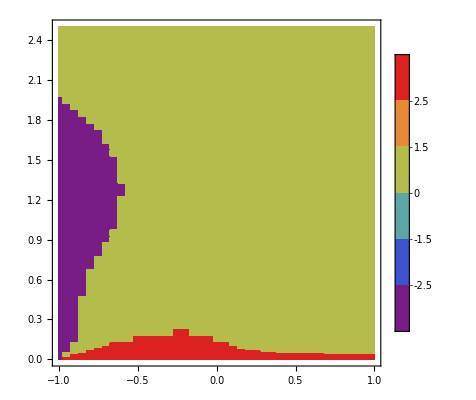
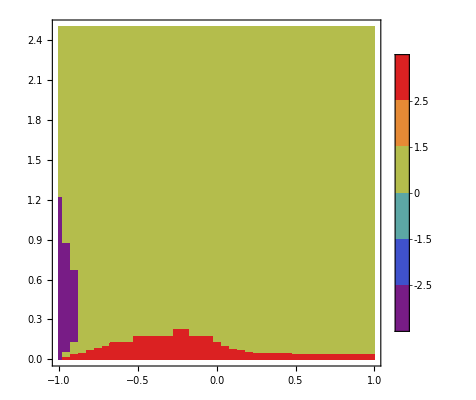
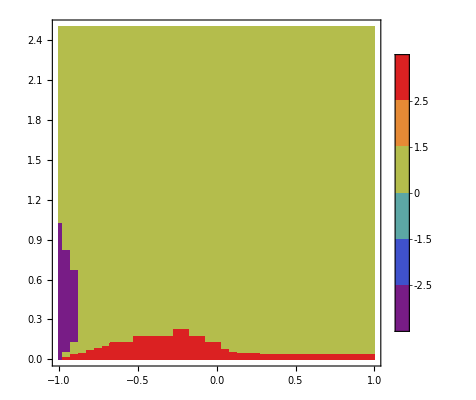

```mathematica
Table[ListContourPlot[dataOptTest⟦ik,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{ik,1,Length[TabKH]}]
```

## ContourPlot

```mathematica
listcolor=Reverse[Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[TabKH]-1)}]]
```

{RGBColor[1., 0.820127, 0.126955],RGBColor[1., 0.6815686, 0.08952772],RGBColor[0.9819778, 0.48442019999999997, 0.05144122],RGBColor[0.9108294, 0.27453859999999997, 0.020955220000000004],RGBColor[0.7514516, 0.09778, 0.006329439999999999],RGBColor[0.468742, 0., 0.0158236]}

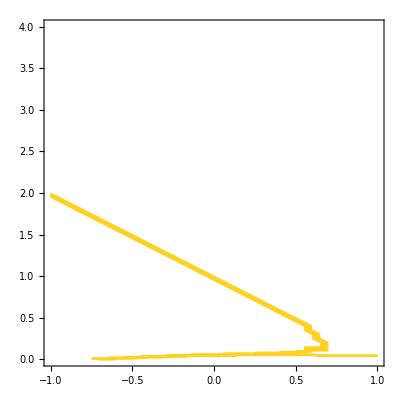
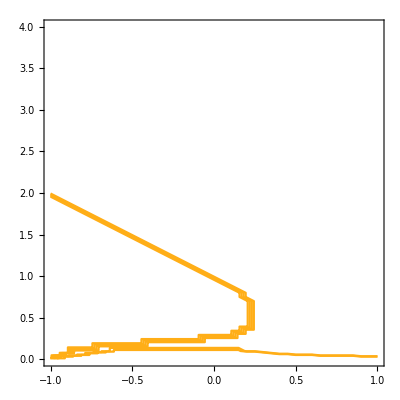
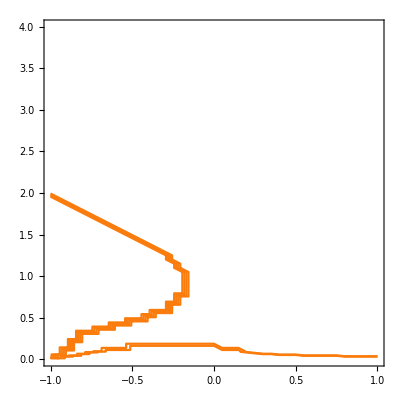
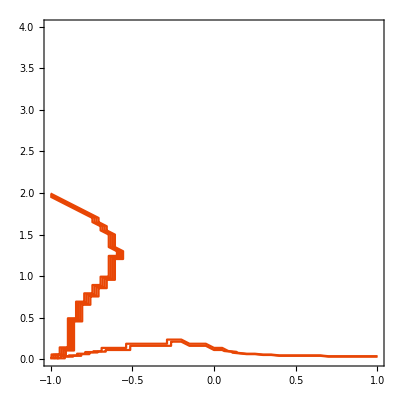
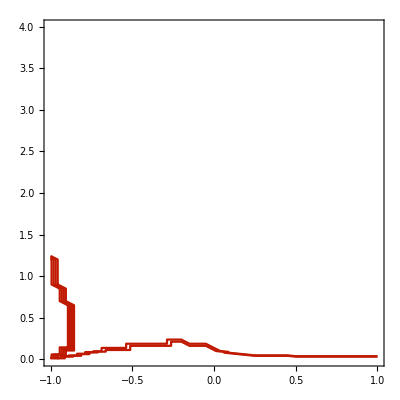
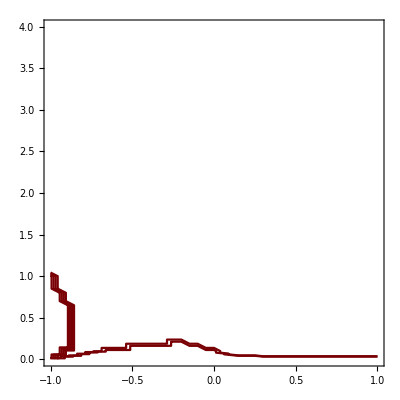

```mathematica
Table[ListContourPlot[dataOptTest[[ik,1]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}]
```

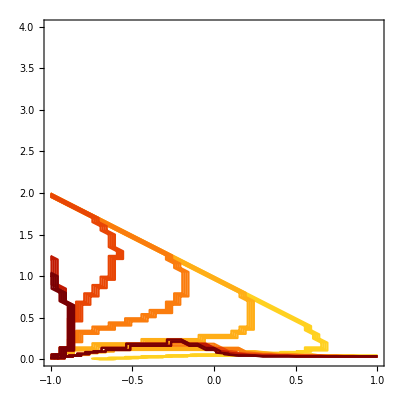

```mathematica
Show[Table[ListContourPlot[dataOptTest[[ik,1]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}]]
```

```mathematica
SensiRH=ResultatA[[1,3]];
```

```mathematica
SensiMH=ResultatA[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

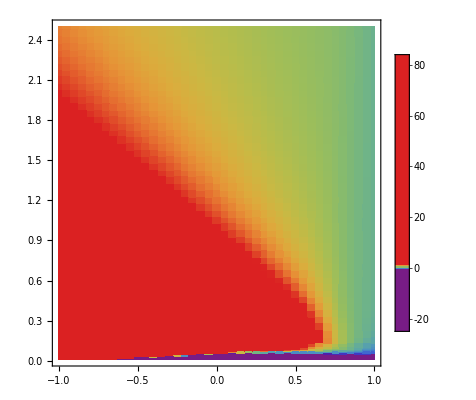
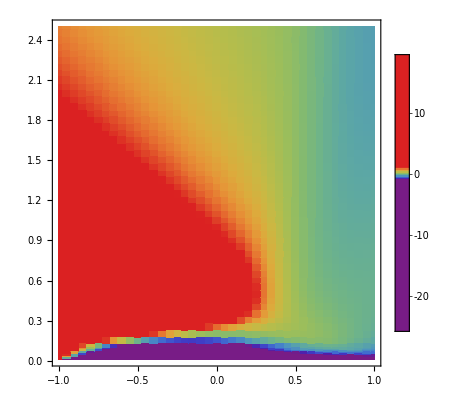
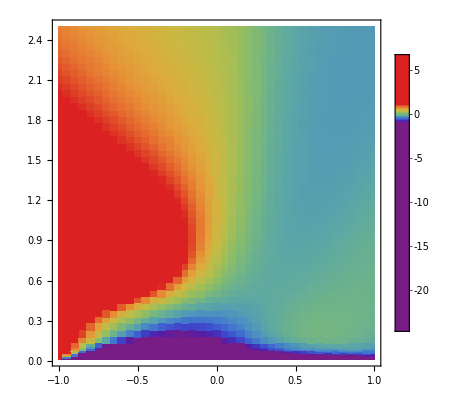
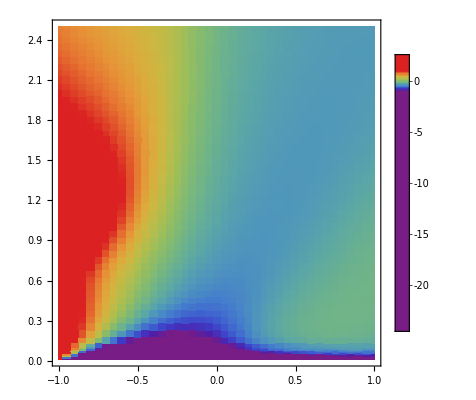
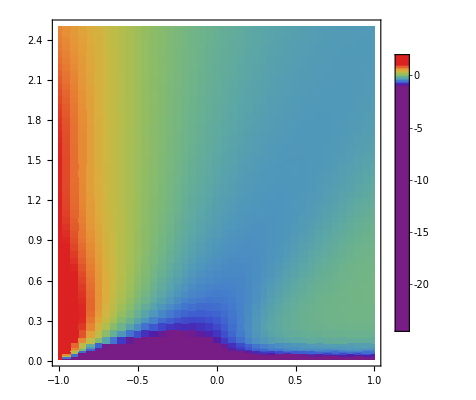
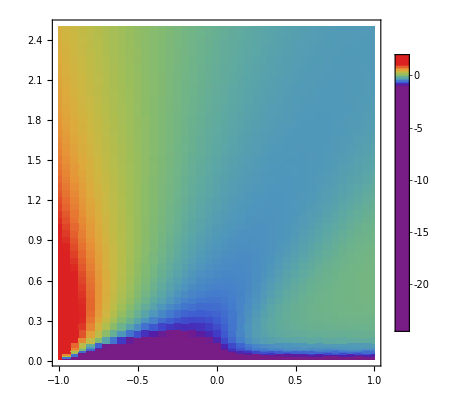

```mathematica
Table[ListDensityPlot[dataSensiRatio[[ik,1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-1,1}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],{ik,1,Length[TabKH]}]
```

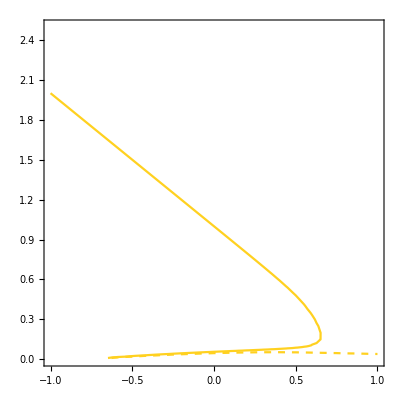
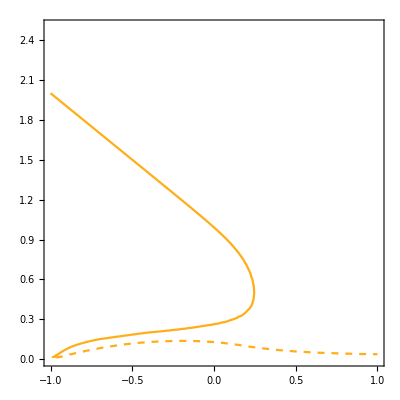
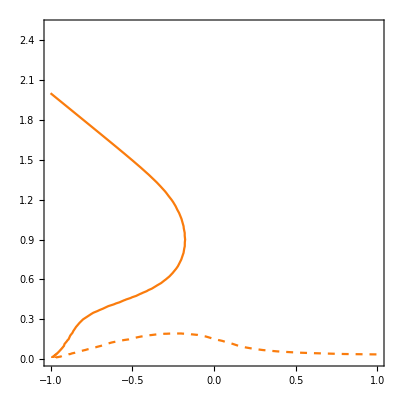
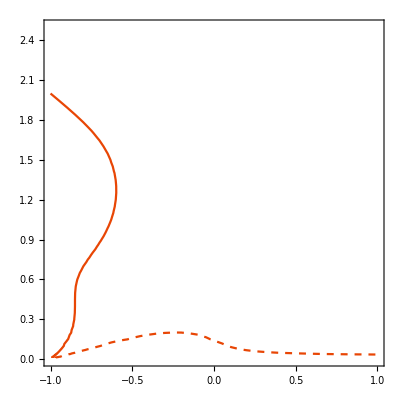
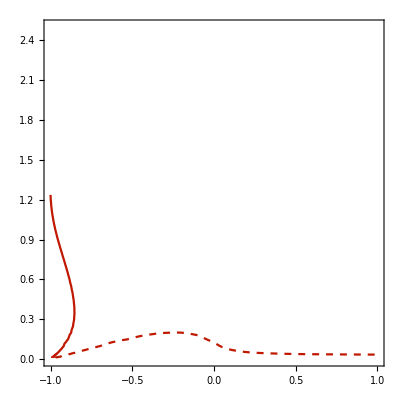
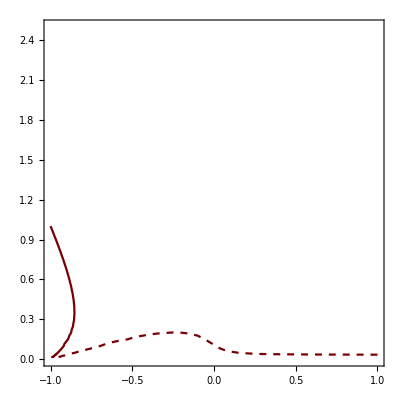

```mathematica
Table[Show[ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}},PerformanceGoal->"Quality"],ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{ik,1,Length[TabKH]}]
```

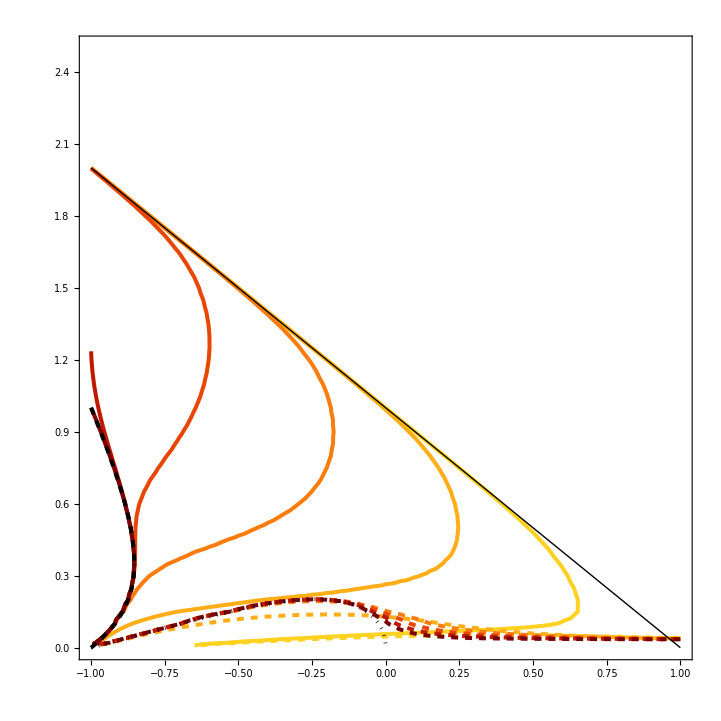

```mathematica
Show[Table[Show[ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}},PerformanceGoal->"Quality"],ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{ik,1,Length[TabKH]}],Limits,Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]
```

## Supplementary figure 4 - panel A

```mathematica
Lambda=ResultatA[[1,2]];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],Lambda[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

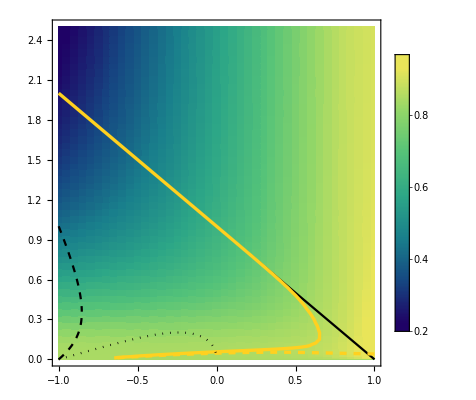

```mathematica
Show[ListDensityPlot[dataLambda⟦1,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.22,0.93}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],ListContourPlot[dataSensiRatio[[1,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[1]],Thickness[0.006],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[1,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[1]],Thickness[0.006],Opacity[1],Dashed],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],Limits,LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

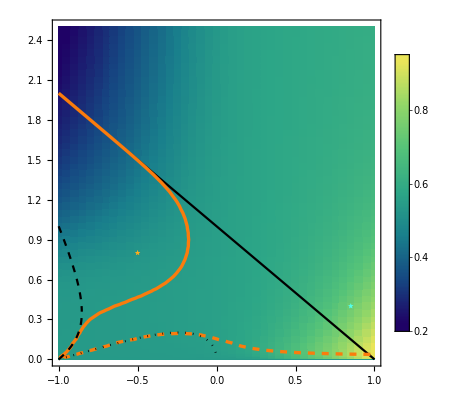

```mathematica
Show[ListDensityPlot[dataLambda⟦3,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.22,0.93}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],ListContourPlot[dataSensiRatio[[3,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[3]],Thickness[0.006],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[3,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[3]],Thickness[0.006],Opacity[1],Dashed],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],ListPlot[{{-0.5,0.8}},PlotMarkers->{Style[★,Large,RGBColor[1., 0.68, 0.1]]},PlotStyle->PointSize[Large]],ListPlot[{{0.85,0.4}},PlotMarkers->{Style[★,Large,RGBColor[0.33, 1., 0.92]]},PlotStyle->PointSize[Large]],Limits,LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

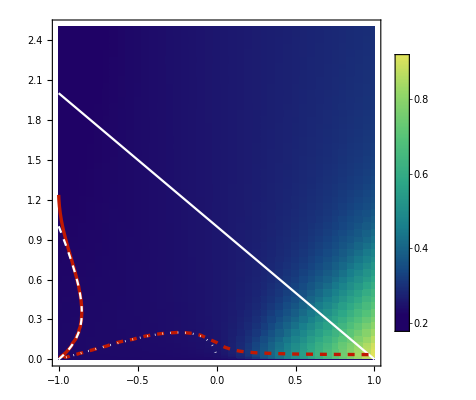

```mathematica
Show[ListDensityPlot[dataLambda⟦5,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.22,0.93}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[White,Thick]],ListContourPlot[dataSensiRatio[[5,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[5]],Thickness[0.006],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[5,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[5]],Thickness[0.006],Opacity[1],Dashed],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],Show[Plot[m/.Sol2[[1]],{rho,-1,0},PlotRange->{{-1,1},{0,2.5}},PlotStyle->Directive[White,Dotted,Thickness[0.004]]],Plot[{m/.Sol[[1]],m/.Sol[[2]],m/.Sol[[3]]},{rho,-1,0},PlotRange->{{-1,1},{0,2.5}},PlotStyle->Directive[White,Dashed,Thickness[0.004]]]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

## Supplementary figure 4 - panel B

```mathematica
Solu1 = NDSolve[sys/.{re->1,rh-> 0.85,me->0.4,mh->0.4,k->10^-7,nH0->0,nE0->1},{nE,nH},{t,0,100},MaxStepSize->0.0001]
```

{{nE→InterpolatingFunction[{{0., 100.}}, <>],nH→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
Solu2= NDSolve[sys/.{re->1,rh-> -0.5,me->0.8,mh->0.8,k->10^-7,nH0->0,nE0->1},{nE,nH},{t,0,100},MaxStepSize->0.0001]
```

{{nE→InterpolatingFunction[{{0., 100.}}, <>],nH→InterpolatingFunction[{{0., 100.}}, <>]}}

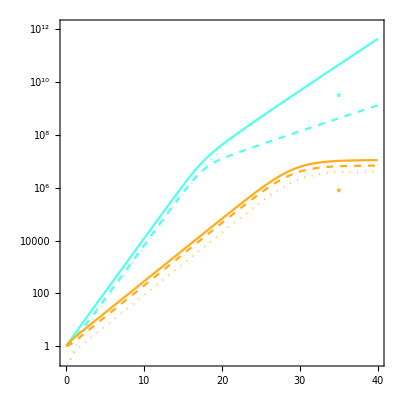

```mathematica
Show[LogPlot[{(nE[t]+nH[t])/.Solu1,(nE[t])/.Solu1,(nH[t])/.Solu1,(nE[t]+nH[t])/.Solu2,(nE[t])/.Solu2,(nH[t])/.Solu2},{t,0,40},Frame->True,PlotStyle->{RGBColor[0.33, 1., 0.92],Directive[RGBColor[0.33, 1., 0.92],Dashed],Directive[Dotted,RGBColor[0.33, 1., 0.92]],RGBColor[1., 0.68, 0.1],Directive[Dashed,RGBColor[1., 0.68, 0.1]],Directive[RGBColor[1., 0.68, 0.1],Dotted]},PlotRange->{All,{10^-0.5,10^12.1}},AspectRatio->1,LabelStyle->{FontSize->18,FontFamily->"Arial",Black},FrameTicks->{{{{10^0,"10^0"},{10^3,"10^3"},{10^6,"10^6"},{10^9,"10^9"},{10^12,"10^12"}},None},{Automatic,None}}],ListLogPlot[{{35,10^5.9}},PlotMarkers->{Style[★,Large,RGBColor[1., 0.68, 0.1]]},PlotStyle->PointSize[Large]],ListLogPlot[{{35,10^9.5}},PlotMarkers->{Style[★,Large,RGBColor[0.33, 1., 0.92]]},PlotStyle->PointSize[Large]]]
```

## Supplementary figure 5 - panel A

```mathematica
tmaxB = {30};
NE0 =0;
NH0 = 1;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.1,0.005}],Table[i,{i,0.15,2,0.025}]}];
TabKH =10^-{10,8,6,4,2};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatB=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatB[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{1}
 |  |  |  |

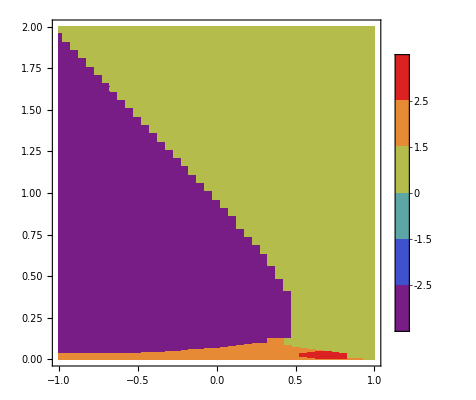
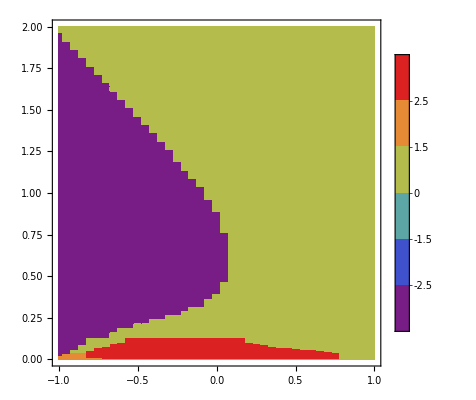
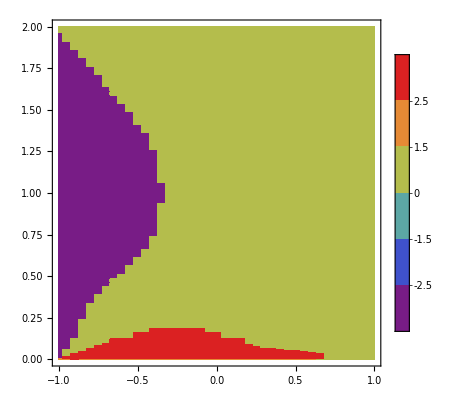
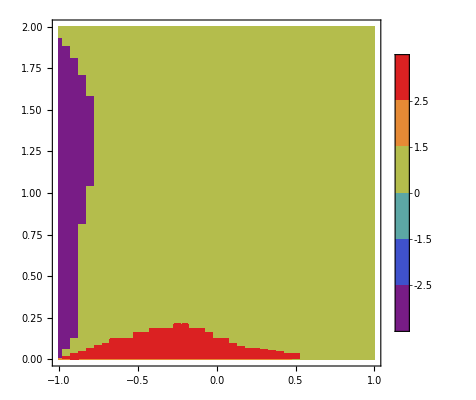
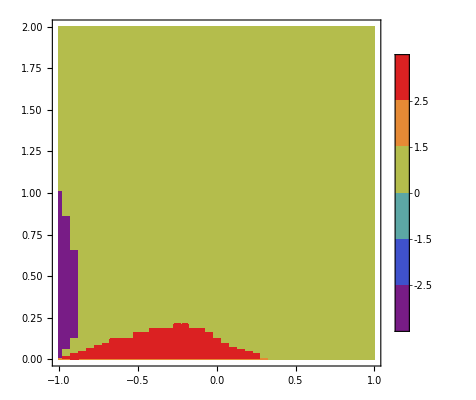

```mathematica
Table[ListContourPlot[dataOptTest⟦ik,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{ik,1,Length[TabKH]}]
```

## ContourPlot

```mathematica
listcolor=Reverse[Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[TabKH]-1)}]]
```

{RGBColor[1., 0.820127, 0.126955],RGBColor[1., 0.646929, 0.0801709],RGBColor[0.969963, 0.376081, 0.0322881],RGBColor[0.822129, 0.122225, 0.0039559],RGBColor[0.468742, 0., 0.0158236]}

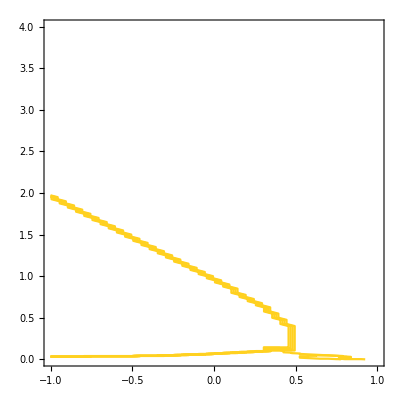
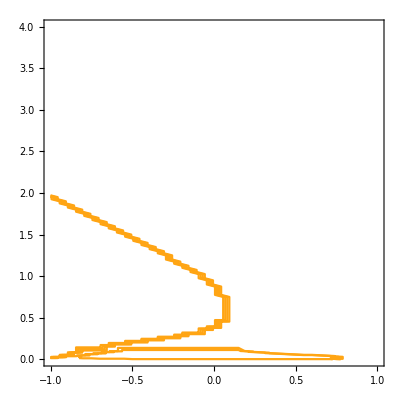
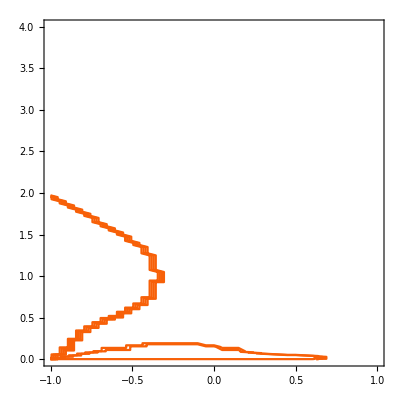
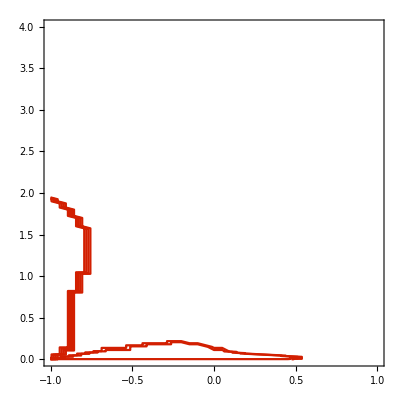
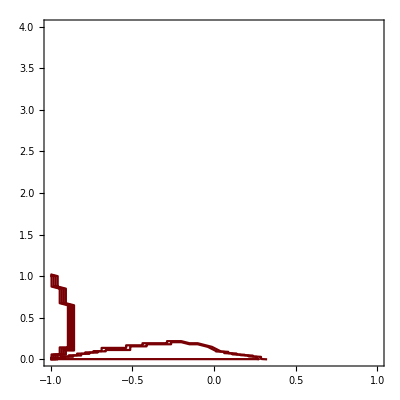

```mathematica
Table[ListContourPlot[dataOptTest[[ik,1]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}]
```

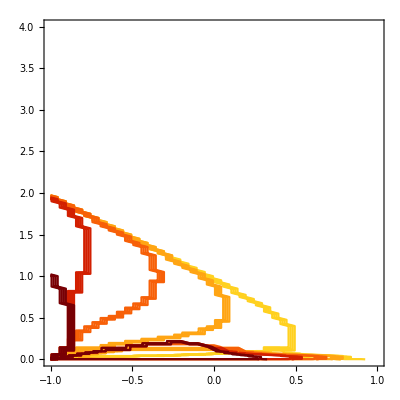

```mathematica
Show[Table[ListContourPlot[dataOptTest[[ik,1]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}]]
```

```mathematica
SensiRH=ResultatB[[1,3]];
```

```mathematica
SensiME=ResultatB[[1,4]];
```

```mathematica
SensiMH=ResultatB[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiRatio2=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiME[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

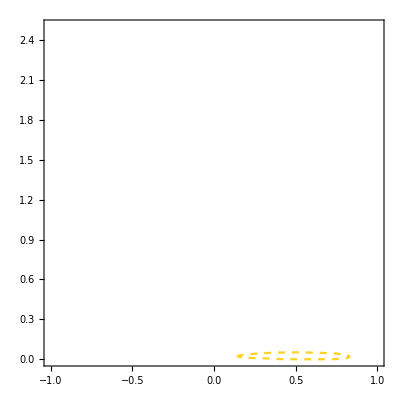
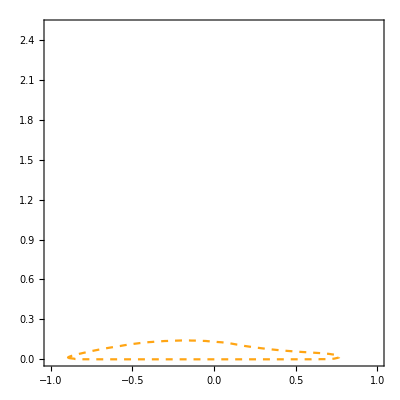
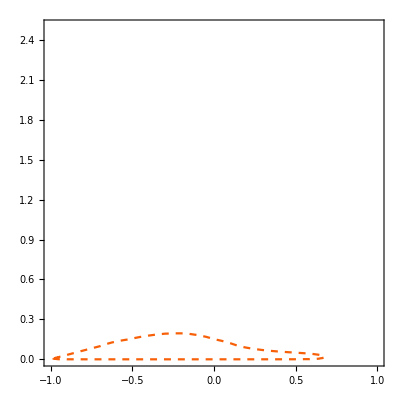
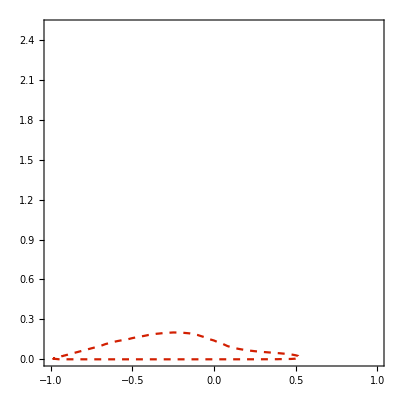
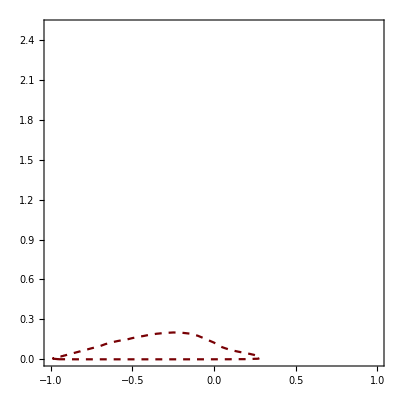

```mathematica
Table[Show[ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{ik,1,Length[TabKH]}]
```

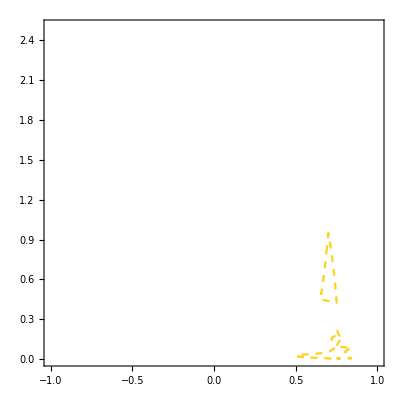
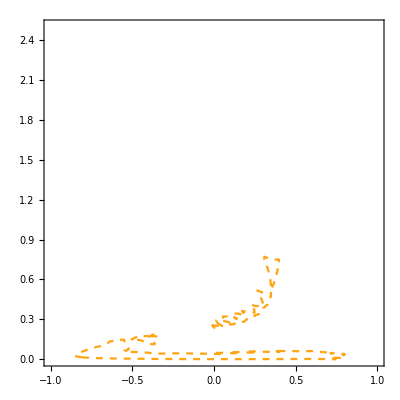
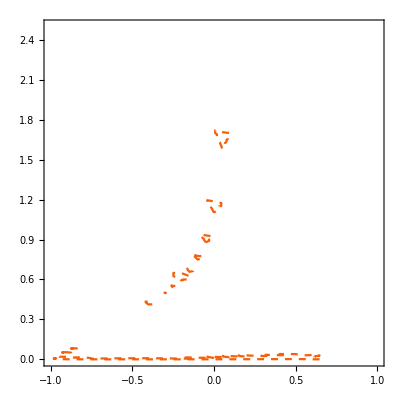
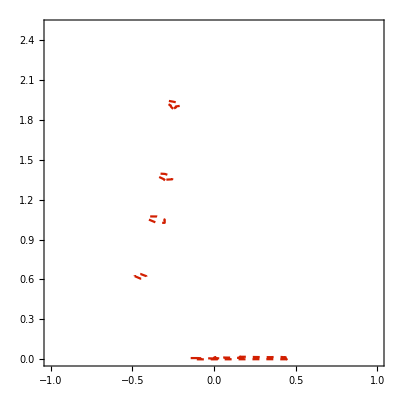
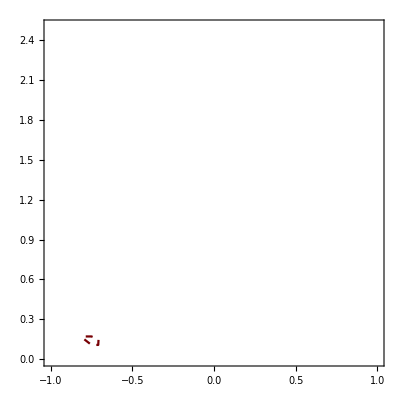

```mathematica
Table[Show[ListContourPlot[dataSensiRatio2[[ik,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{ik,1,Length[TabKH]}]
```

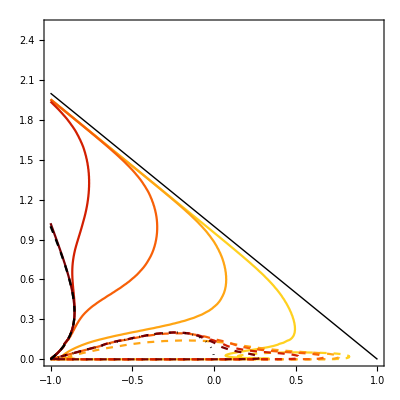

```mathematica
Show[Table[Show[ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{ik,1,Length[TabKH]}],Limits,Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

## Supplementary figure 5 - panel B

```mathematica
tmaxB = {20,25,30,35,40,50,60};
NE0 =1;
NH0 = 0;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.15,2.5,0.05}]}];
TabKH =10^-{7};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatC=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatC[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{{1}}
 |  |  |  |

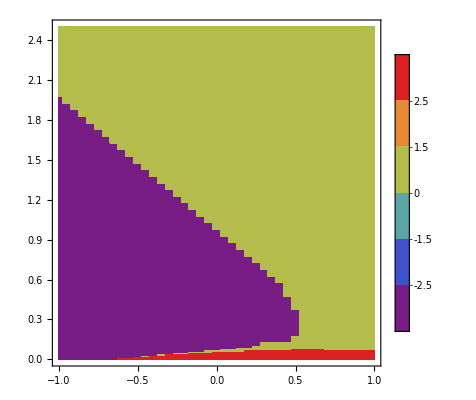
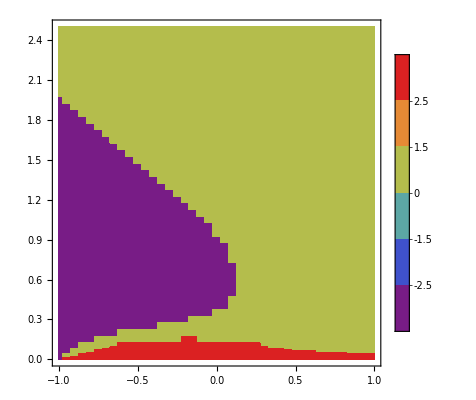
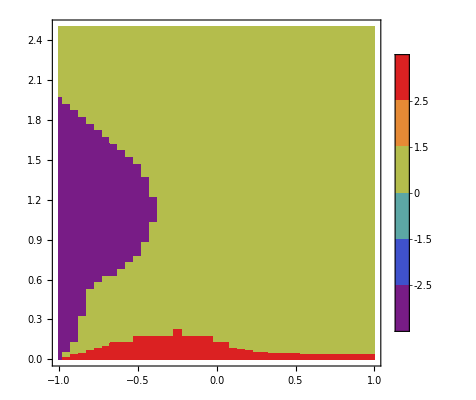
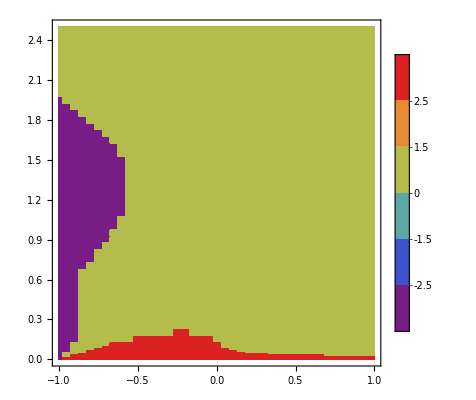
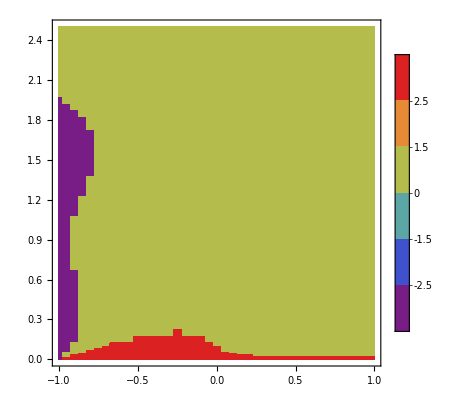
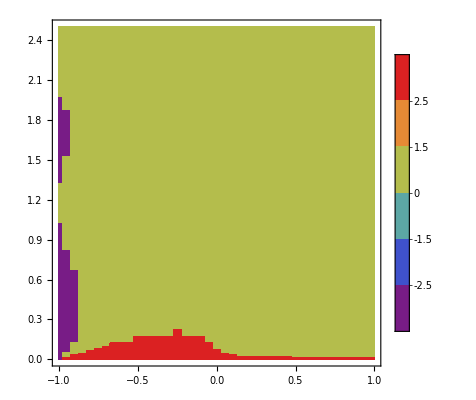
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListContourPlot[dataOptTest⟦1,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

#### Contour Plot

```mathematica
listcolor=Reverse[Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]]
```

{RGBColor[0.914809, 0.897673, 0.350652],RGBColor[0.571909, 0.839991, 0.408102],RGBColor[0.329526, 0.762208, 0.474596],RGBColor[0.175507, 0.652273, 0.528496],RGBColor[0.097699, 0.498132, 0.548165],RGBColor[0.0839935, 0.279645, 0.510102],RGBColor[0.122103, 0.00901808, 0.39826]}

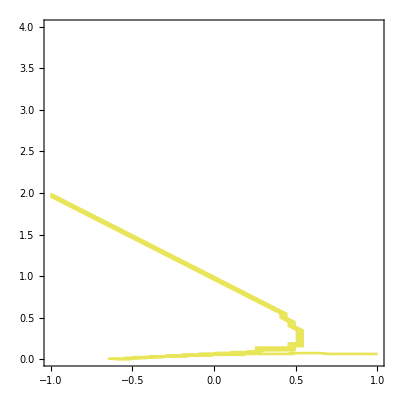
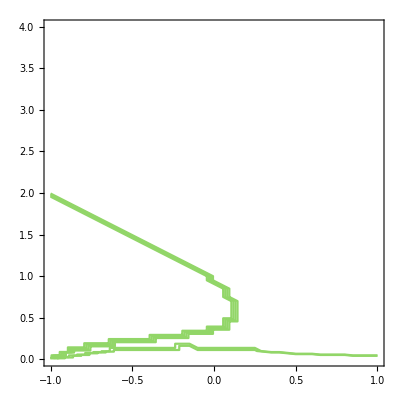
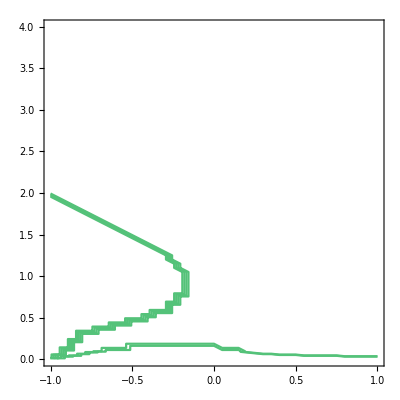
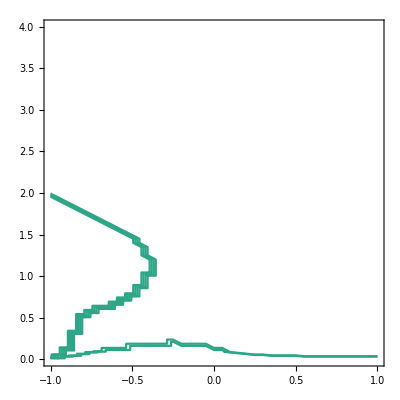
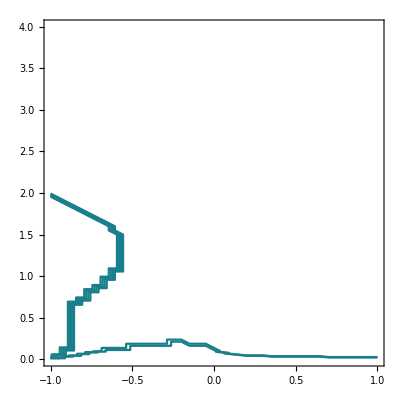
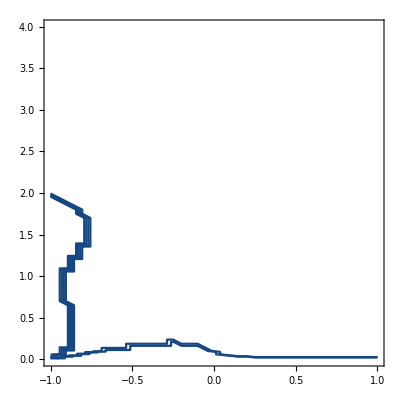
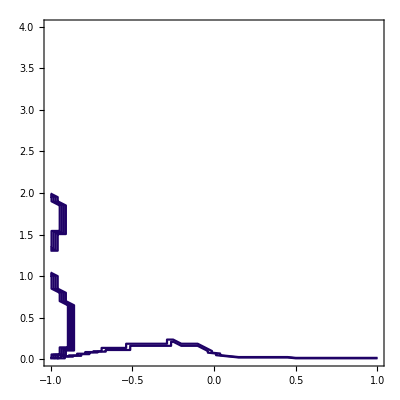

```mathematica
Table[ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}]
```

```mathematica
SensiRH=ResultatC[[1,3]];
```

```mathematica
SensiME=ResultatC[[1,4]];
```

```mathematica
SensiMH=ResultatC[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
dataSensiRatio2=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiME[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

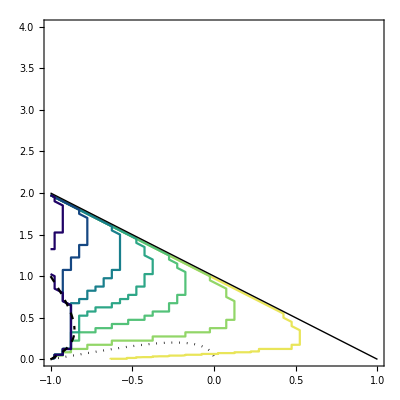

```mathematica
Show[Table[ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}],Limits,Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]
```

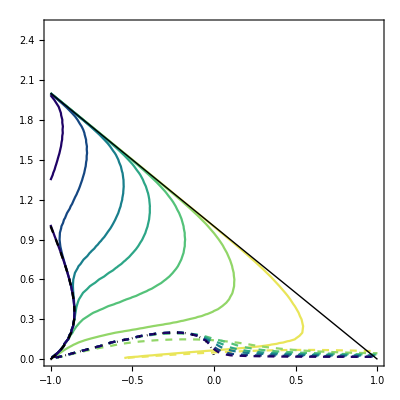

```mathematica
Show[Table[Show[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],Limits,LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

## Supplementary figure 5 - panel C

```mathematica
tmaxB = {20,25,30,35,40,50,60};
NE0 =0;
NH0 = 1;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.15,2.5,0.05}]}];
TabKH =10^-{7};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatD=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatD[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{{{{-1.,0.,2},{-1.,0.01,2},{-1.,0.02,2},{-1.,0.03,2},{-1.,0.04,2},{-1.,0.05,2},{-1.,0.06,-3},{-1.,0.07,-3},{-1.,0.08,-3},{-1.,0.09,-3},{-1.,0.1,-3},{-1.,0.15,-3},2395,{1.,1.95,1},{1.,2.,1},{1.,2.05,1},{1.,2.1,1},{1.,2.15,1},{1.,2.2,1},{1.,2.25,1},{1.,2.3,1},{1.,2.35,1},{1.,2.4,1},{1.,2.45,1},{1.,2.5,1}},5,{1}}}
 |  |  |  |

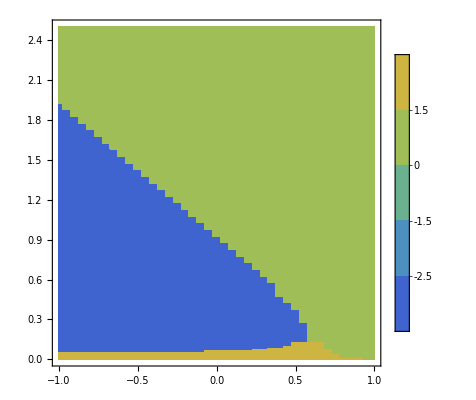
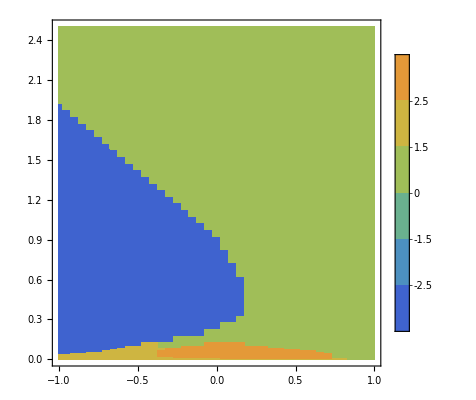
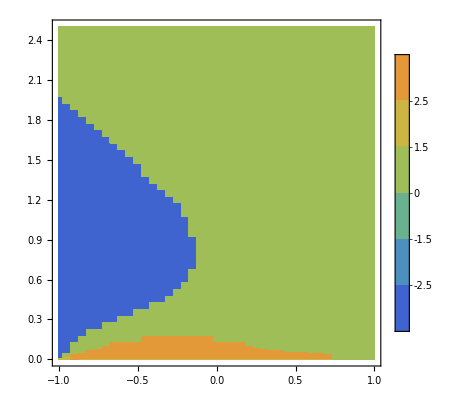
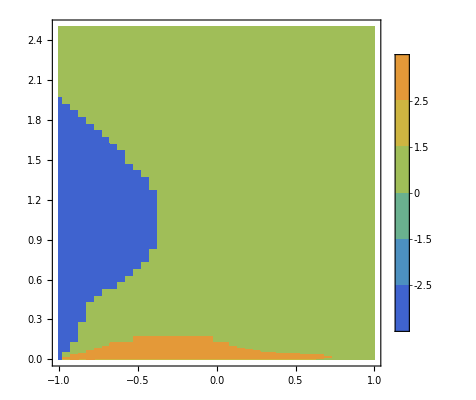
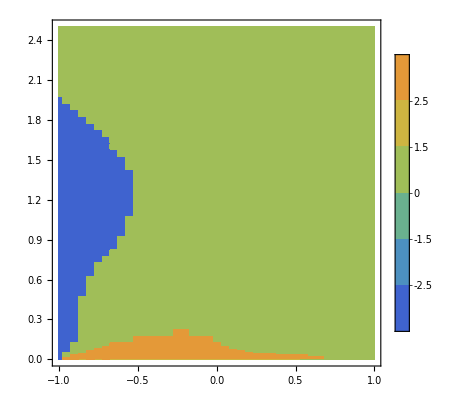
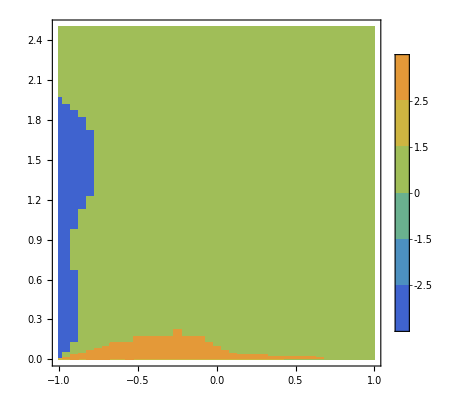
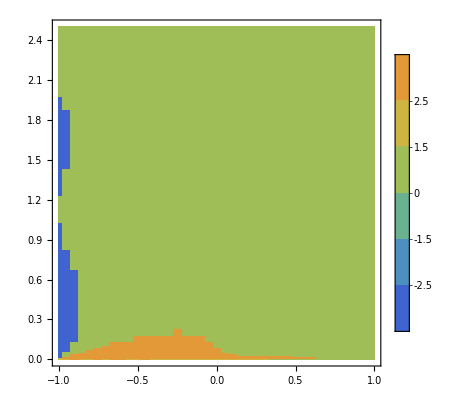

```mathematica
Table[ListContourPlot[dataOptTest⟦1,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

#### Contour Plot

```mathematica
listcolor=Reverse[Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]]
```

{RGBColor[0.914809, 0.897673, 0.350652],RGBColor[0.571909, 0.839991, 0.408102],RGBColor[0.329526, 0.762208, 0.474596],RGBColor[0.175507, 0.652273, 0.528496],RGBColor[0.097699, 0.498132, 0.548165],RGBColor[0.0839935, 0.279645, 0.510102],RGBColor[0.122103, 0.00901808, 0.39826]}

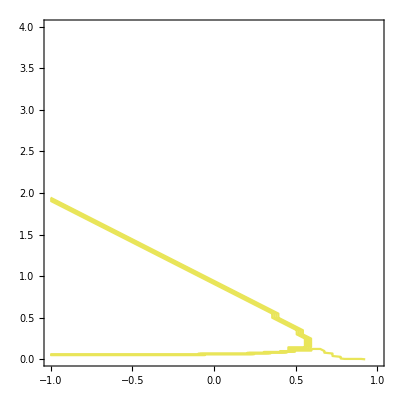
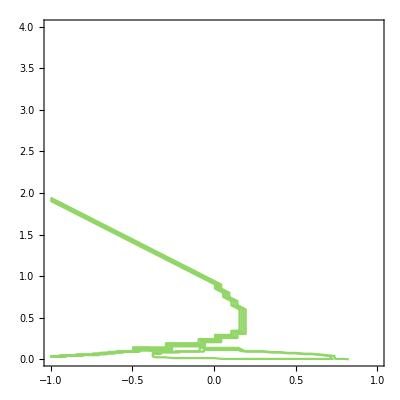
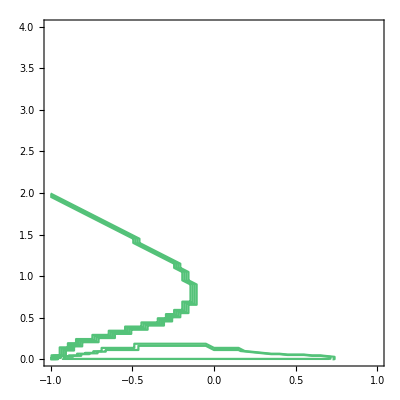
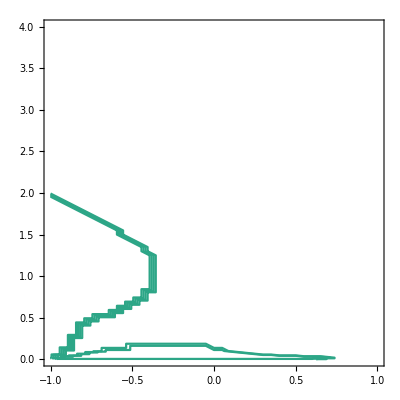
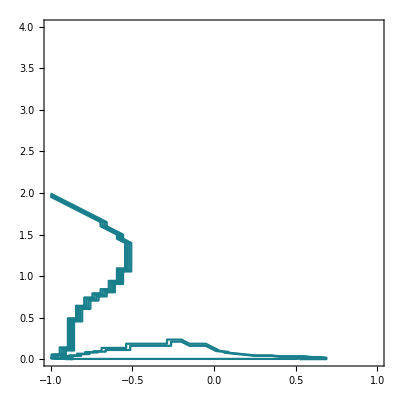
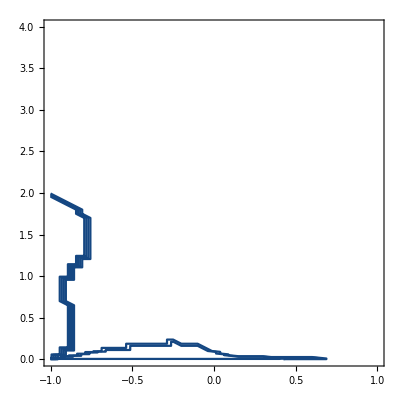
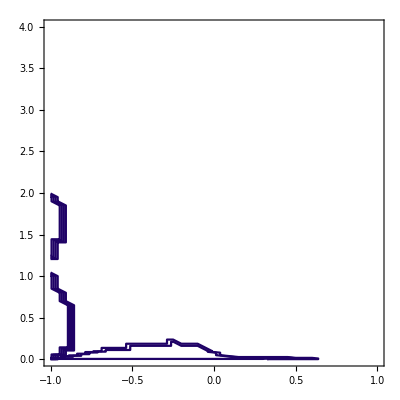

```mathematica
Table[ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}]
```

```mathematica
SensiRH=ResultatD[[1,3]];
```

```mathematica
SensiME=ResultatD[[1,4]];
```

```mathematica
SensiMH=ResultatD[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiRatio2=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiME[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

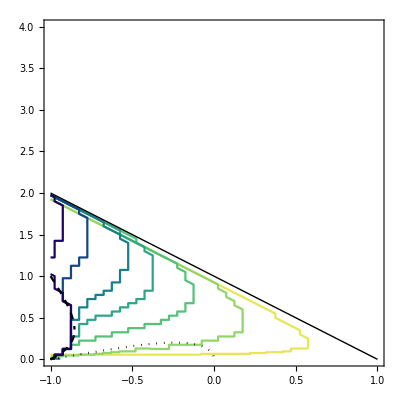

```mathematica
Show[Table[ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}],Limits,Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]
```

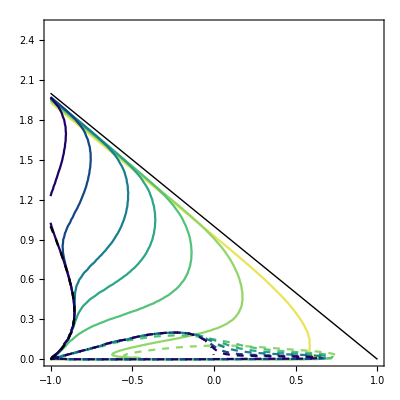

```mathematica
Show[Table[Show[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],Limits,LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

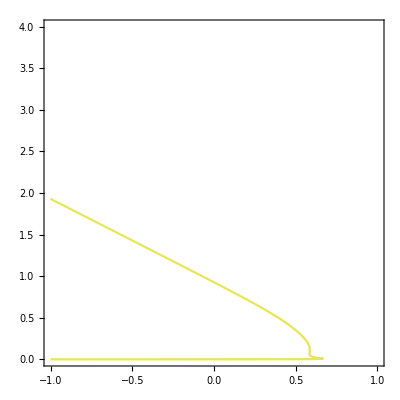
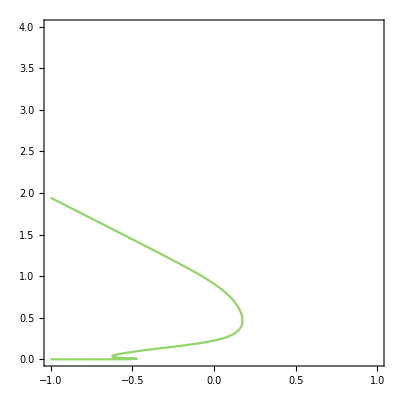
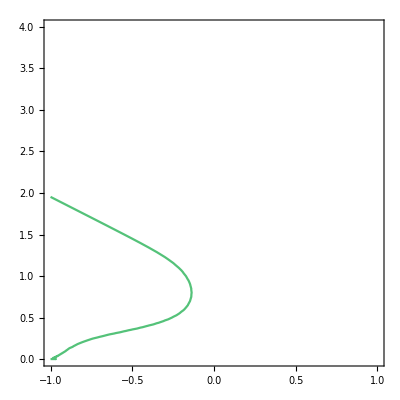
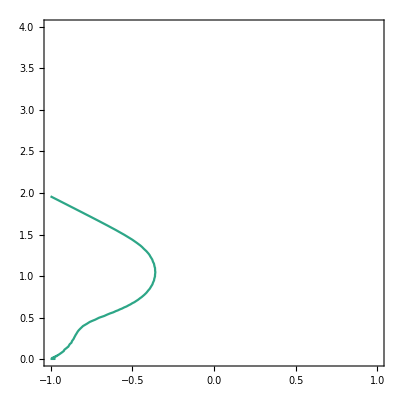
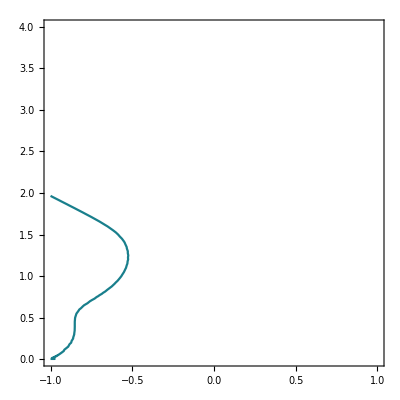
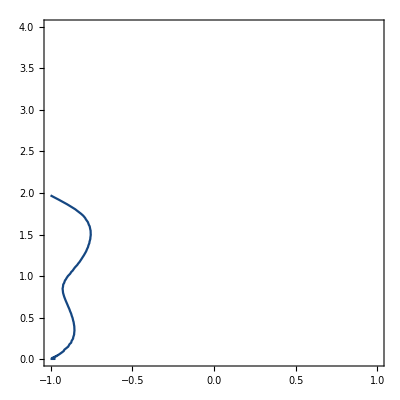
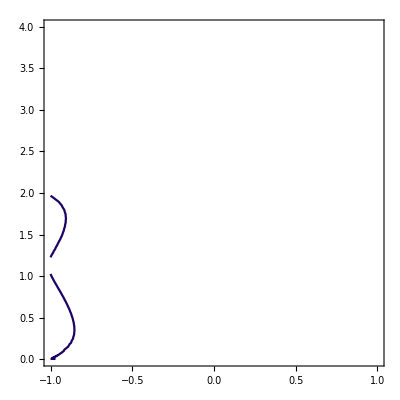

```mathematica
Table[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}]
```

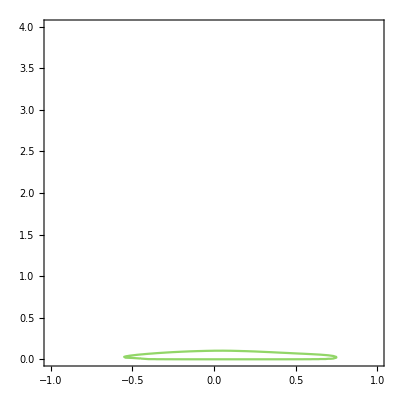
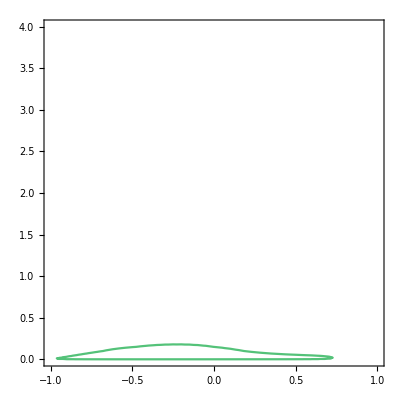
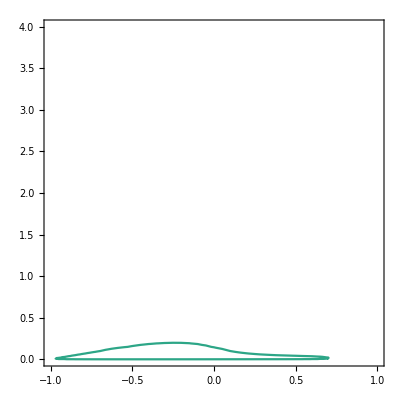
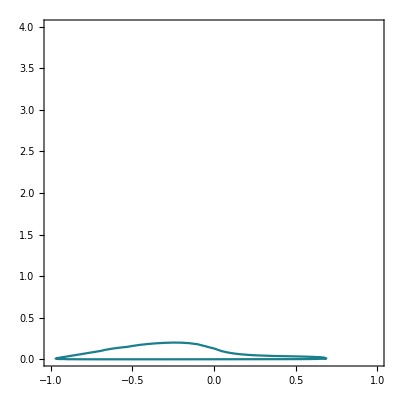
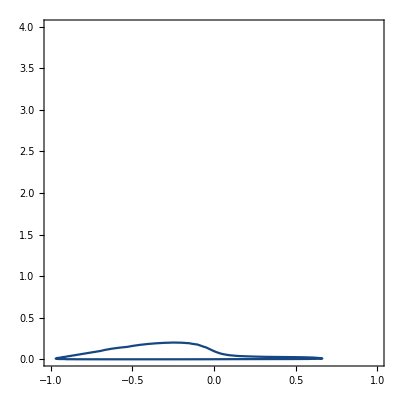
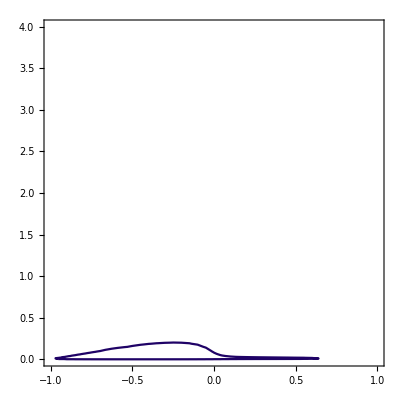
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}]
```